```mathematica
Middle[tuple_]:= tuple[[IntegerPart[(Length[tuple]+1)/2]]]
```

```mathematica
MyMatrix[p_,q_,max_] := Module[
{ current, result, digitp, digitq},
result = Array[0&,{p,q}];
Monitor[
For[current=0, current < max, current++,
digitp = Middle[IntegerDigits[current,p]]+1;
digitq = Middle[IntegerDigits[current,q]]+1;
result[[digitp, digitq]] =result[[digitp, digitq]] + 1
],
ToString[current] <> "/" <> ToString[max]
];
Return [result];
]
```

-0.0115153

1.92586

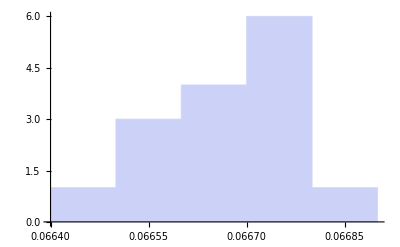

```mathematica
With[
{p=3,q=5,max=(3*5)^6},
With[
{l=Flatten[Map[#/max&,MyMatrix[p,q,max]]]},
Print[N [Skewness[l]]];
Print[N[Kurtosis[l]]];
Histogram[l]
]
]
```

```mathematica
With[
{p=3,q=5,max=(3*5)^8},
With[
{l=Flatten[Map[#/max&,MyMatrix[p,q,max]]]},
Print[N [Skewness[l]]];
Print[N[Kurtosis[l]]];
Histogram[l]
]
]
```

```mathematica
(3*5)^8
```

2562890625